21

{1+1/2 (-1-ξ),(1+ξ)/2}

{{Null,Null},{Null,Null}}

{{20.0167,-19.9917},{-19.9917,20.0167}}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

21

0

0

0.0025

0.0475

{1,0}

{1,0}

{0,1}

{0,1}

{0.,0.00743775,0.014769,0.0218872,0.0286849,0.0350541,0.0408858,0.0460694,0.0504929,0.0540422,0.0566012,0.0580513,0.058271,0.0571358,0.0545178,0.0502854,0.044303,0.0364306,0.0265235,0.0144317,0.}

{0.}

{0.,0.00743775,0.00743775,0.014769,0.014769,0.0218872,0.0218872,0.0286849,0.0286849,0.0350541,0.0350541,0.0408858,0.0408858,0.0460694,0.0460694,0.0504929,0.0504929,0.0540422,0.0540422,0.0566012,0.0566012,0.0580513,0.0580513,0.058271,0.058271,0.0571358,0.0571358,0.0545178,0.0545178,0.0502854,0.0502854,0.044303,0.044303,0.0364306,0.0364306,0.0265235,0.0265235,0.0144317,0.0144317,0.}

{}

{y[x]→-(ⅇ^-x (-ⅇ+ⅇ^(1+2 x)+ⅇ^x x-ⅇ^(2+x) x))/(-1+ⅇ^2)}

-(ⅇ^-x (-ⅇ+ⅇ^(1+2 x)+ⅇ^x x-ⅇ^(2+x) x))/(-1+ⅇ^2)

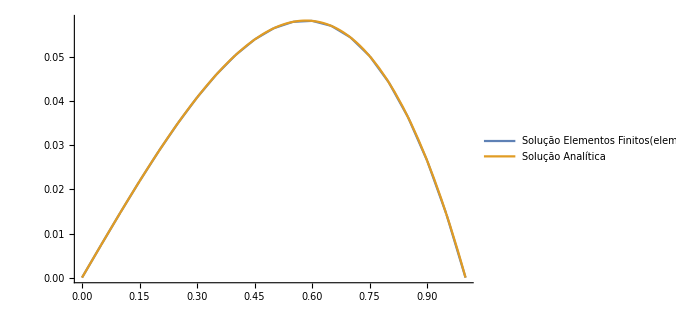

0.00214729

0.0761874

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
GaussQ[g_,n_,a_,b_]:=Total[g[First[#]]*Last[#]&/@GaussianQuadratureWeights[n,a,b]]
α=1;γ=1;
u0=0;u1=0;
n=20;h=1/n;np=4;m=n+1
f[x_]:=x
φ={InterpolatingPolynomial[{{-1,1},{1,0}},ξ],InterpolatingPolynomial[{{-1,0},{1,1}},ξ]}
K={{,},{,}}
K=α*(2/h)*Table[GaussQ[D[φ[[r]],ξ]*D[φ[[s]],ξ]/.ξ->#&,np,-1,1],{r,2},{s,2}]+γ*(h/2)*Table[GaussQ[φ[[r]]*φ[[s]]/.ξ->#&,np,-1,1],{r,2},{s,2}]

F1=ConstantArray[0,{n+1}]
For[i=1,i<m,i=i+1,
F1[[i;;i+1]]=F1[[i;;i+1]]+(h/2)*Table[GaussQ[((f[x]/.x->(h*(i-1)+h/2*(ξ+1)))*φ[[r]])/.ξ->#&,np,-1,1],{r,2}]

]
K1=ConstantArray[0,{n+1,n+1}]
For[i=1,i<m,i=i+1,
K1[[i;;i+1,i;;i+1]]=K1[[i;;i+1,i;;i+1]]+K

]

m=n+1
F1[[1]]=u0
F1[[m]]=u1
F1[[2]]=F1[[2]]-K1[[2,1]]*u0
F1[[m-1]]=F1[[m-1]]-K1[[m-1,m]]*u1
K1[[1,1;;2]]={1,0}
K1[[1;;2,1]]={1,0}
K1[[m,m-1;;m]]={0,1}
K1[[m-1;;m,m]]={0,1}

w=LinearSolve[K1,F1]
LagrangeP[p1_]:={Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h,1}},x],p1<=x≤p1+h}},0]}
W1={w[[1]]}
For[i=2,i<m,i++,
W1=Join[W1,ConstantArray[w[[i]],{2}]]
]
W1=Join[W1,{w[[m]]}]
ϕ={}
For[i=1,i<=n,i++,
AppendTo[ϕ,LagrangeP[(i-1)*h][[1]]];
AppendTo[ϕ,LagrangeP[(i-1)*h][[2]]]
]

Uh[x_]:=W1.ϕ
solution=DSolve[{-α*y''[x]+γ*y[x]==f[x],y[0]==0,y[1]==0},y[x],x][[1]]
u[x_]=y[x]/.solution[[1]]
G7=Plot[{Uh[x],u[x]},{x,0,1},PlotRange->All,ImageSize->500,AxesStyle->Black,ImageSize->400,PlotLegends->{"Solução Elementos Finitos(elementos lineares)","Solução Analítica"}]
G[x_]:=(u[x]-Uh[x])^2
(Sum[h/2*Sum[GaussianQuadratureWeights[4,-1,1][[l]][[2]]*(G[x]/.x->(i*h+h/2*(GaussianQuadratureWeights[4,-1,1][[l]][[1]]+1))),{l,1,4}],{i,0,n}])^(1/2)
G1[x_]:=(D[u[x],x]-D[Uh[x],x])^2
(Sum[h/2*Sum[GaussianQuadratureWeights[4,-1,1][[l]][[2]]*(G1[x]/.x->(i*h+h/2*(GaussianQuadratureWeights[4,-1,1][[l]][[1]]+1))),{l,1,4}],{i,0,n}])^(1/2)
```

```mathematica
Export["1Linear_n10.png",G7]
```

1Linear_n10.png